## 第四章

```mathematica
(*1*)
Series[Log[x],{x,1,5}]
Series[Log[x],{x,1,6}]
Series[Log[x],{x,1,7}]
Series[Log[x],{x,1,8}]
Series[Log[x],{x,1,9}]
Series[Log[x],{x,1,10}]
```

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5+O[x-1]^6

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5-1/6 (x-1)^6+O[x-1]^7

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5-1/6 (x-1)^6+1/7 (x-1)^7+O[x-1]^8

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5-1/6 (x-1)^6+1/7 (x-1)^7-1/8 (x-1)^8+O[x-1]^9

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5-1/6 (x-1)^6+1/7 (x-1)^7-1/8 (x-1)^8+1/9 (x-1)^9+O[x-1]^10

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5-1/6 (x-1)^6+1/7 (x-1)^7-1/8 (x-1)^8+1/9 (x-1)^9-1/10 (x-1)^10+O[x-1]^11

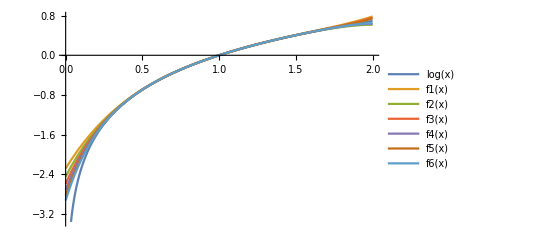

```mathematica
f1[x_]=(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5;
f2[x_]=(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5-1/6 (x-1)^6;
f3[x_]=(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5-1/6 (x-1)^6+1/7 (x-1)^7;
f4[x_]=(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5-1/6 (x-1)^6+1/7 (x-1)^7-1/8 (x-1)^8;
f5[x_]=(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5-1/6 (x-1)^6+1/7 (x-1)^7-1/8 (x-1)^8+1/9 (x-1)^9;
f6[x_]=(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5-1/6 (x-1)^6+1/7 (x-1)^7-1/8 (x-1)^8+1/9 (x-1)^9-1/10 (x-1)^10;
Plot[{Log[x],f1[x],f2[x],f3[x],f4[x],f5[x],f6[x]},{x,0,2},PlotLegends->"Expressions"]
```

```mathematica
Clear["`*"]
```

```mathematica
Series[1/(3-x),{x,1,2}]
Series[1/(3-x),{x,1,3}]
Series[1/(3-x),{x,1,4}]
Series[1/(3-x),{x,1,5}]
Series[1/(3-x),{x,1,6}]
```

1/2+(x-1)/4+1/8 (x-1)^2+O[x-1]^3

1/2+(x-1)/4+1/8 (x-1)^2+1/16 (x-1)^3+O[x-1]^4

1/2+(x-1)/4+1/8 (x-1)^2+1/16 (x-1)^3+1/32 (x-1)^4+O[x-1]^5

1/2+(x-1)/4+1/8 (x-1)^2+1/16 (x-1)^3+1/32 (x-1)^4+1/64 (x-1)^5+O[x-1]^6

1/2+(x-1)/4+1/8 (x-1)^2+1/16 (x-1)^3+1/32 (x-1)^4+1/64 (x-1)^5+1/128 (x-1)^6+O[x-1]^7

```mathematica
f[x]=1/(3-x);
```

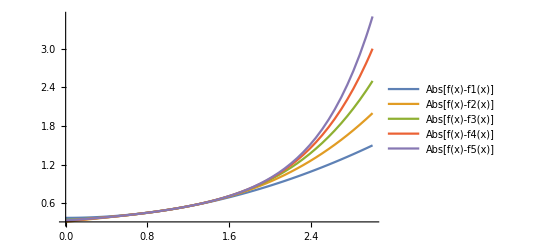

```mathematica
f1[x_]:=f[x]-(1/2+(x-1)/4+1/8 (x-1)^2);
f2[x_]:=f[x]-(1/2+(x-1)/4+1/8 (x-1)^2+1/16 (x-1)^3);
f3[x_]:=f[x]-(1/2+(x-1)/4+1/8 (x-1)^2+1/16 (x-1)^3+1/32 (x-1)^4);
f4[x_]:=f[x]-(1/2+(x-1)/4+1/8 (x-1)^2+1/16 (x-1)^3+1/32 (x-1)^4+1/64 (x-1)^5);
f5[x_]:=f[x]-(1/2+(x-1)/4+1/8 (x-1)^2+1/16 (x-1)^3+1/32 (x-1)^4+1/64 (x-1)^5+1/128 (x-1)^6);
Plot[{Abs[f[x]-f1[x]],Abs[f[x]-f2[x]],Abs[f[x]-f3[x]],Abs[f[x]-f4[x]],Abs[f[x]-f5[x]]},{x,0,3},PlotLegends->"Expressions"]
```